### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[642296934875]
```

<|Index→642296934875,QCode→24344244342242333,RuleSet→{A→BC,CB→A,B→AAAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

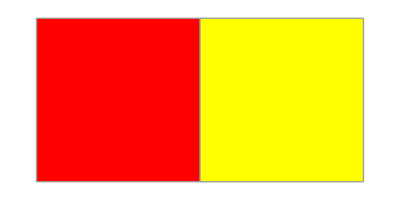
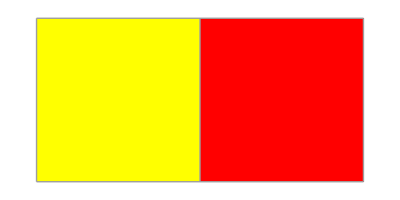

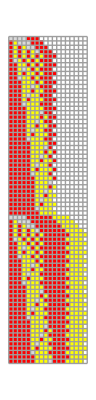
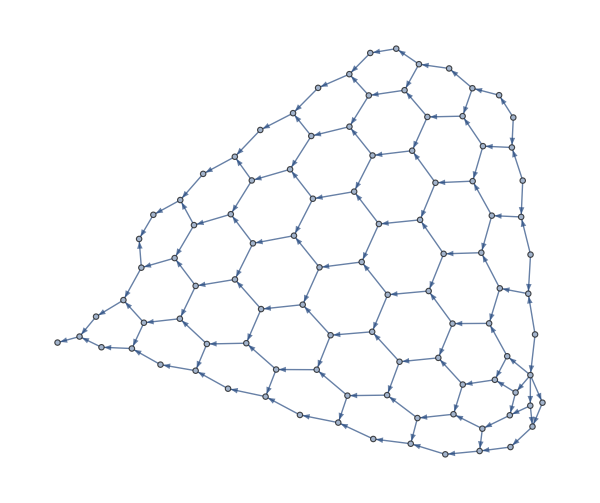
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "AAAABBB",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
SSSInteractiveDisplay[sss]
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,1→3,1→4,1→5,2→6,3→6,6→7,3→8,4→8,8→9,«1457»,792→994,994→995,989→996,995→996,996→997,991→998,997→998,998→999,993→1000,999→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},{1},{1},{1},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1},{1},{1},{1},{1},{1},{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1},{1},{1},{1},{1},{1},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1},{1},{1},{1},{1},{1},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1},{1},{1},{1},{1},{1},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1},{1},{1},{1},{1},{1},{178},{1,2,3,4},{4,184},{3,5},{4,8},{7,13},{1},{3,196},{1},{1,5},{1},{5,200},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1},{1},{},{1,2,3,4},{4},{3,5},{4,8},{7,13},{1},{3},{1},{1,5},{1},{5},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{7,178}]
```

{{479},{487},{495},{503},{511},{519},{527},{535},{543},{551},{559},{567},{575},{583},{591},{599},{607},{615}}

```mathematica
nds[[1;;615]]
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},{1},{1},{1},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1},{1},{1},{1},{1},{1},{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1},{1},{1},{1},{1},{1},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1},{1},{1},{1},{1},{1},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1},{1},{1},{1},{1},{1},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;615]]]
```

```mathematica
{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},€^5[{1}],{34},

{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},€^2[{1},{1,7}],€^2[{1},{7,58},€^3[{1},{1,7}]],{1},{7,58},€^7[{1}],{58},

{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},€^2[{1},{1,7}],€^5[{1},{7,82},€^3[{1},{1,7}]],{1},{7,82},€^7[{1}],{82},

{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},€^2[{1},{1,7}],€^8[{1},{7,106},€^3[{1},{1,7}]],{1},{7,106},€^7[{1}],{106},

{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},€^2[{1},{1,7}],€^11[{1},{7,130},€^3[{1},{1,7}]],{1},{7,130},€^7[{1}],{130},

{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},€^2[{1},{1,7}],€^14[{1},{7,154},€^3[{1},{1,7}]],{1},{7,154},€^7[{1}],{154},

{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},€^2[{1},{1,7}],€^17[{1},{7,178},€^3[{1},{1,7}]],{1},{7,178}}
```

```mathematica
Position[rsl,{1,2,3,4}]
```

{{1},{14},{31},{48},{65},{82},{99}}

```mathematica
Flatten@%
```

{1,14,31,48,65,82,99}

```mathematica
Differences@%
```

{13,17,17,17,17,17}

```mathematica
rsl[[82;;98]]//ExpandAll
```

{{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154}}

```mathematica
rsl[[14;;30]]
```

{{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},€^2[{1},{1,7}],€^2[{1},{7,58},€^3[{1},{1,7}]],{1},{7,58},€^7[{1}],{58}}

```mathematica
ps=Position[rsl[[82;;98]],_Integer]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{3,1},{3,2},{4,1},{4,2},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{9,1},{9,2},{10,1},{11,1},{11,2},{12,1,1},{12,2,1},{12,2,2},{12,3},{13,1,1},{13,2,1},{13,2,2},{13,3,1,1},{13,3,2,1},{13,3,2,2},{13,3,3},{13,4},{14,1},{15,1},{15,2},{16,1,1},{16,2},{17,1}}

```mathematica
Extract[#,ps]& /@ Partition[rsl[[14;;98]],17]
```

{{1,2,3,4,4,40,3,5,4,8,7,13,1,3,52,1,1,5,1,5,56,1,1,7,2,1,7,58,1,1,7,3,2,1,7,58,1,7,58},{1,2,3,4,4,64,3,5,4,8,7,13,1,3,76,1,1,5,1,5,80,1,1,7,2,1,7,82,1,1,7,3,5,1,7,82,1,7,82},{1,2,3,4,4,88,3,5,4,8,7,13,1,3,100,1,1,5,1,5,104,1,1,7,2,1,7,106,1,1,7,3,8,1,7,106,1,7,106},{1,2,3,4,4,112,3,5,4,8,7,13,1,3,124,1,1,5,1,5,128,1,1,7,2,1,7,130,1,1,7,3,11,1,7,130,1,7,130},{1,2,3,4,4,136,3,5,4,8,7,13,1,3,148,1,1,5,1,5,152,1,1,7,2,1,7,154,1,1,7,3,14,1,7,154,1,7,154}}

```mathematica
%//Transpose
```

{{1,1,1,1,1},{2,2,2,2,2},{3,3,3,3,3},{4,4,4,4,4},{4,4,4,4,4},{40,64,88,112,136},{3,3,3,3,3},{5,5,5,5,5},{4,4,4,4,4},{8,8,8,8,8},{7,7,7,7,7},{13,13,13,13,13},{1,1,1,1,1},{3,3,3,3,3},{52,76,100,124,148},{1,1,1,1,1},{1,1,1,1,1},{5,5,5,5,5},{1,1,1,1,1},{5,5,5,5,5},{56,80,104,128,152},{1,1,1,1,1},{1,1,1,1,1},{7,7,7,7,7},{2,2,2,2,2},{1,1,1,1,1},{7,7,7,7,7},{58,82,106,130,154},{1,1,1,1,1},{1,1,1,1,1},{7,7,7,7,7},{3,3,3,3,3},{2,5,8,11,14},{1,1,1,1,1},{7,7,7,7,7},{58,82,106,130,154},{1,1,1,1,1},{7,7,7,7,7},{58,82,106,130,154}}

```mathematica
FindSequenceFunction[#,k]& /@ %
```

{1,2,3,4,4,8 (2+3 k),3,5,4,8,7,13,1,3,4 (7+6 k),1,1,5,1,5,8 (4+3 k),1,1,7,2,1,7,2 (17+12 k),1,1,7,3,-1+3 k,1,7,2 (17+12 k),1,7,2 (17+12 k)}

```mathematica
% /. k->k-1 //FullSimplify
```

{1,2,3,4,4,-8+24 k,3,5,4,8,7,13,1,3,4+24 k,1,1,5,1,5,8+24 k,1,1,7,2,1,7,10+24 k,1,1,7,3,-4+3 k,1,7,10+24 k,1,7,10+24 k}

```mathematica
ReplacePart[rsl[[82;;98]],Thread[ps->%145]]
```

{{1,2,3,4},{4,24 k-8},{3,5},{4,8},{7,13},{1},{3,24 k+4},{1},{1,5},{1},{5,24 k+8},€^2[{1},{1,7}],€^(3 k-4)[{1},{7,24 k+10},€^3[{1},{1,7}]],{1},{7,24 k+10},€^7[{1}],{24 k+10}}

```mathematica
rsl[[82;;98]]/. {136->24k-8,148->24k+4,152->24k+8,154->24k+10,14->3k-4}//InputForm
```

{{1, 2, 3, 4}, {4, -8 + 24*k}, {3, 5}, {4, 8}, {7, 13}, {1}, {3, 4 + 24*k}, {1}, {1, 5}, {1}, {5, 8 + 24*k}, 
 IndexedConcatenate[{1}, {1, 7}, 2], IndexedConcatenate[{1}, {7, 10 + 24*k}, IndexedConcatenate[{1}, {1, 7}, 3], -4 + 3*k], {1}, 
 {7, 10 + 24*k}, IndexedConcatenate[{1}, 7], {10 + 24*k}}

```mathematica
%36==%146
```

True

```mathematica
ans={IndexedConcatenate[
{1,2,3,4},{4,-8+24*k},{3,5},{4,8},{7,13},{1},{3,4+24*k},{1},{1,5},{1},{5,8+24*k},IndexedConcatenate[{1},{1,7},2],IndexedConcatenate[{1},{7,10+24*k},IndexedConcatenate[{1},{1,7},3],-4+3*k],{1},{7,10+24*k},IndexedConcatenate[{1},7],{10+24*k}
,{k,6,6}]};
ans//ExpandAll
```

{{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154}}

```mathematica
%165==rsl[[82;;98]]//ExpandAll
```

False

```mathematica
Length/@{%165,rsl[[82;;98]]//ExpandAll}
```

{137,137}

```mathematica
Equal@@%& /@Transpose[{%165,rsl[[82;;98]]//ExpandAll}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Union@%
```

{True}

```mathematica
%165
```

```mathematica
Grid@Transpose@{%165,rsl[[82;;98]]//ExpandAll}
```

{1,2,3,4} | {1,2,3,4}
{4,136} | {4,136}
{3,5} | {3,5}
{4,8} | {4,8}
{7,13} | {7,13}
{1} | {1}
{3,148} | {3,148}
{1} | {1}
{1,5} | {1,5}
{1} | {1}
{5,152} | {5,152}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{1,7} | {1,7}
{1} | {1}
{7,154} | {7,154}
{1} | {1}
{1} | {1}
{1} | {1}
{1} | {1}
{1} | {1}
{1} | {1}
{1} | {1}
{154} | {154}

```mathematica
nds
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},{1},{1},{1},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1},{1},{1},{1},{1},{1},{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1},{1},{1},{1},{1},{1},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1},{1},{1},{1},{1},{1},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1},{1},{1},{1},{1},{1},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1},{1},{1},{1},{1},{1},{178},{1,2,3,4},{4,184},{3,5},{4,8},{7,13},{1},{3,196},{1},{1,5},{1},{5,200},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1},{1},{},{1,2,3,4},{4},{3,5},{4,8},{7,13},{1},{3},{1},{1,5},{1},{5},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1}}

```mathematica
SequencePosition[nds,ans//ExpandAll]
```

{}

```mathematica
nds//Short
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},«973»,{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1}}

Not a great success. Try by hand.

```mathematica
rsl[[8]]
```

€_(n$3⊨1)^3[€_(n$1⊨1)^2[{3-3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-2+n$2+3 n$3},€_(n$1⊨1)^(-4+n$2+3 n$3)[{1,-3+n$1+n$2+3 n$3,-2+n$1+n$2+3 n$3}],{-6+2 n$2+6 n$3,-5+2 n$2+6 n$3,-4+2 n$2+6 n$3},€_(n$1⊨1)^(-1+3 n$3)[€^2[{-3-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-1+n$2+3 n$3},€_(n$1⊨1)^(-3+n$2+3 n$3)[{1,-2+n$1+n$2+3 n$3,-1+n$1+n$2+3 n$3}],{-4+2 n$2+6 n$3,-3+2 n$2+6 n$3,-2+2 n$2+6 n$3},€_(n$1⊨1)^(3 n$3)[€^2[{-1-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{-1+3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,n$2+3 n$3},€_(n$1⊨1)^(-2+n$2+3 n$3)[{1,-1+n$1+n$2+3 n$3,n$1+n$2+3 n$3}],{-2+2 n$2+6 n$3,-1+2 n$2+6 n$3,2 n$2+6 n$3},€_(n$1⊨1)^(1+3 n$3)[€^2[{1-n$1+2 n$2+6 n$3}]]]]

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}
```

```mathematica
€_(k⊨1)^3[
€_(i⊨1)^2[{9 k i-3 i-6 k+3}],
€_(j⊨1)^2[{1,j+3 k-2},€_(i⊨1)^(j+3 k-4)[{1,i+j+3 k-3,i+j+3 k-2}],{2 j+6 k-6,2 j+6 k-5,2 j+6 k-4},€_(i⊨1)^(3 k-1)[€^2[{-i+2 j+6 k-3}]]],
€_(i⊨1)^2[{9 i k-6 k+1}],
€_(j⊨1)^2[{1,j+3 k-1},€_(i⊨1)^(j+3 k-3)[{1,i+j+3 k-2,i+j+3 k-1}],{2 j+6 k-4,2 j+6 k-3,2 j+6 k-2},€_(i⊨1)^(3 k)[€^2[{-i+2 j+6 k-1}]]],
€_(i⊨1)^2[{9 k i+3 i-6 k-1}],
€_(j⊨1)^2[{1,j+3 k},€_(i⊨1)^(j+3 k-2)[{1,i+j+3 k-1,i+j+3 k}],{2 j+6 k-2,2 j+6 k-1,2 j+6 k},€_(i⊨1)^(3 k+1)[€^2[{-i+2 j+6 k+1}]]]]
```

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}//InputForm
```

IndexedConcatenate[IndexedConcatenate[{3 - 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -2 + j + 3*k}, 
  IndexedConcatenate[{1, -3 + i + j + 3*k, -2 + i + j + 3*k}, {i, 1, -4 + j + 3*k}], {-6 + 2*j + 6*k, -5 + 2*j + 6*k, -4 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-3 - i + 2*j + 6*k}, 2], {i, 1, -1 + 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{1 - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -1 + j + 3*k}, 
  IndexedConcatenate[{1, -2 + i + j + 3*k, -1 + i + j + 3*k}, {i, 1, -3 + j + 3*k}], {-4 + 2*j + 6*k, -3 + 2*j + 6*k, -2 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-1 - i + 2*j + 6*k}, 2], {i, 1, 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{-1 + 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, j + 3*k}, 
  IndexedConcatenate[{1, -1 + i + j + 3*k, i + j + 3*k}, {i, 1, -2 + j + 3*k}], {-2 + 2*j + 6*k, -1 + 2*j + 6*k, 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{1 - i + 2*j + 6*k}, 2], {i, 1, 1 + 3*k}], {j, 1, 2}], {k, 1, 3}]

Can we do better?

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```